## Mathematica Lab 1 - Solutions

### Exercise 1

```mathematica
Table[i,{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

(a)

```mathematica
Table[i,{i,-3,17}]
```

{-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}

(b)

```mathematica
Table[2i-1,{i,1,100}]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199}

```mathematica
Length[%]
```

100

(c)

```mathematica
Table[Prime[i],{i,1,100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
Select[Table[Prime[i],{i,1,100}],#<100&]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

(d)

```mathematica
step=(1-(-1))/(100-1) (* point pacing is interval length divided by number of intervals *)
Table[-1+(i-1)step,{i,1,100}]
```

2/99

{-1,-97/99,-95/99,-31/33,-91/99,-89/99,-29/33,-85/99,-83/99,-9/11,-79/99,-7/9,-25/33,-73/99,-71/99,-23/33,-67/99,-65/99,-7/11,-61/99,-59/99,-19/33,-5/9,-53/99,-17/33,-49/99,-47/99,-5/11,-43/99,-41/99,-13/33,-37/99,-35/99,-1/3,-31/99,-29/99,-3/11,-25/99,-23/99,-7/33,-19/99,-17/99,-5/33,-13/99,-1/9,-1/11,-7/99,-5/99,-1/33,-1/99,1/99,1/33,5/99,7/99,1/11,1/9,13/99,5/33,17/99,19/99,7/33,23/99,25/99,3/11,29/99,31/99,1/3,35/99,37/99,13/33,41/99,43/99,5/11,47/99,49/99,17/33,53/99,5/9,19/33,59/99,61/99,7/11,65/99,67/99,23/33,71/99,73/99,25/33,7/9,79/99,9/11,83/99,85/99,29/33,89/99,91/99,31/33,95/99,97/99,1}

(e)

```mathematica
Join[Table[x,{x,0,2π,π/4}],Table[x,{x,0,2π,π/6}]]
```

{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π,0,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6,2 π}

```mathematica
Sort[DeleteDuplicates[%]]
```

{0,π/6,π/4,π/3,π/2,(2 π)/3,(3 π)/4,(5 π)/6,π,(7 π)/6,(5 π)/4,(4 π)/3,(3 π)/2,(5 π)/3,(7 π)/4,(11 π)/6,2 π}

### Exercise 2

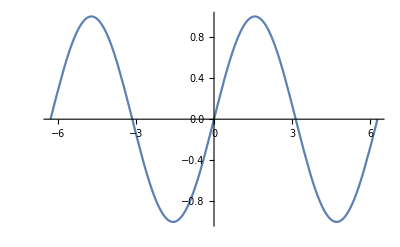

```mathematica
Plot[Sin[x],{x,-2π,2π}]
```

(a)

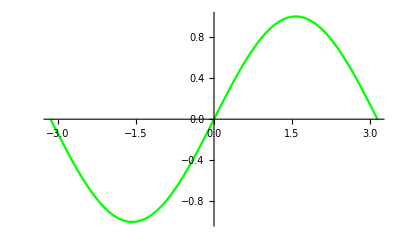

```mathematica
Plot[Sin[x],{x,-π,π},PlotStyle->Green]
```

(b)

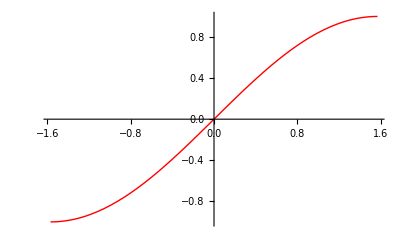

```mathematica
Plot[Sin[x],{x,-π/2,π/2},PlotStyle->Directive[Thick,Red]]
```

(c)

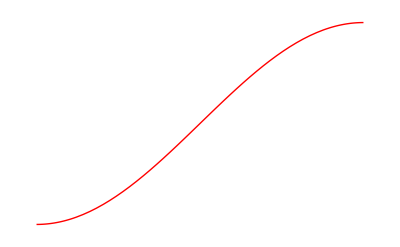

```mathematica
Plot[Sin[x],{x,-π/2,π/2},PlotStyle->Directive[Thick,Red],Axes->None]
```

(d)

```mathematica
xticks=Sort[DeleteDuplicates[Join[Table[x,{x,-π/2,π/2,π/4}],Table[x,{x,-π/2,π/2,π/6}]]]]
```

{0,-π/2,-π/3,-π/4,-π/6,π/6,π/4,π/3,π/2}

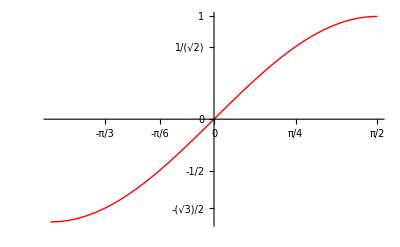

```mathematica
p1=Plot[Sin[x],{x,-π/2,π/2},PlotStyle->Directive[Thick,Red],Ticks->{xticks,Sin[xticks]}]
```

(e)

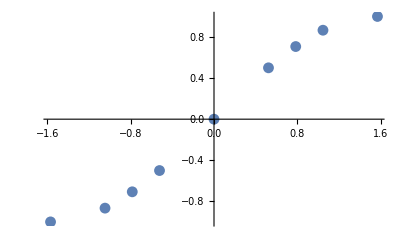

```mathematica
p2=DiscretePlot[Sin[x],{x,xticks},Filling->None]
```

(f)

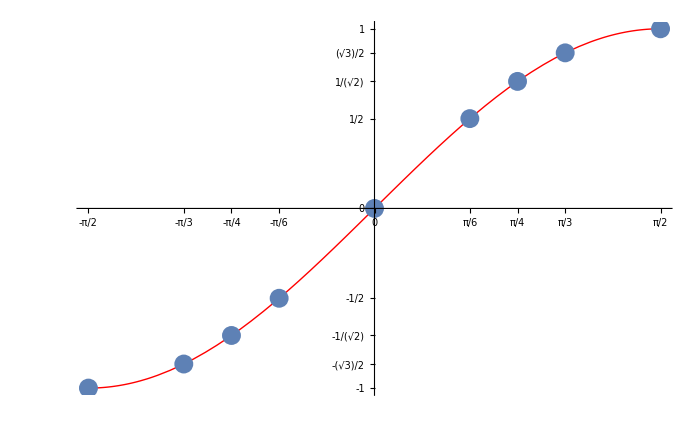

```mathematica
Show[p1,p2,ImageSize->700]
```

### Exercise 3

```mathematica
Series[Cos[x],{x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

```mathematica
c[x_,n_Integer]:=Module[{y},Normal[Series[Cos[y],{y,0,n}]]/.y->x]
```

(a)

```mathematica
Table[c[x,k],{k,0,5}]
```

{1,1,1-x^2/2,1-x^2/2,1-x^2/2+x^4/24,1-x^2/2+x^4/24}

(b)

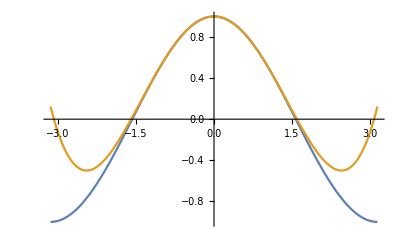

```mathematica
Plot[{Cos[x],c[x,4]},{x,-π,π}]
```

(c)

```mathematica
Manipulate[Plot[{Cos[x],c[x,n]},{x,-2π,2π},PlotRange->{-2,2}],{n,0,20,2}]
```

### Exercise 4

(a)

```mathematica
Solve[z^2-3z+2==0,z]
```

{{z→1},{z→2}}

(b)

```mathematica
Solve[{x+2y-z-u==0,x-y+2z==1,-3x-2y+z+u==-1},{x,y,z}]
```

{{x→1/2,y→1/6 (-1+4 u),z→1/6 (1+2 u)}}

```mathematica
M={{1,2,-1,-1,0},{1,-1,2,0,1},{-3,-2,1,1,-1}}
```

{{1,2,-1,-1,0},{1,-1,2,0,1},{-3,-2,1,1,-1}}

```mathematica
RowReduce[M]
```

{{1,0,0,0,1/2},{0,1,0,-2/3,-1/6},{0,0,1,-1/3,1/6}}

(c)

```mathematica
roots=z/.NSolve[z^55+z^4-z^3+z^2-z-1==0,z]
```

{-1.02149,-1.01409-0.123842 ⅈ,-1.01409+0.123842 ⅈ,-0.991983-0.245727 ⅈ,-0.991983+0.245727 ⅈ,-0.955468-0.363758 ⅈ,-0.955468+0.363758 ⅈ,-0.905058-0.47613 ⅈ,-0.905058+0.47613 ⅈ,-0.841512-0.581144 ⅈ,-0.841512+0.581144 ⅈ,-0.76582-0.677217 ⅈ,-0.76582+0.677217 ⅈ,-0.679199-0.762894 ⅈ,-0.679199+0.762894 ⅈ,-0.583079-0.836864 ⅈ,-0.583079+0.836864 ⅈ,-0.51879,-0.479105-0.897978 ⅈ,-0.479105+0.897978 ⅈ,-0.369161-0.945282 ⅈ,-0.369161+0.945282 ⅈ,-0.255443-0.978083 ⅈ,-0.255443+0.978083 ⅈ,-0.140596-0.996191 ⅈ,-0.140596+0.996191 ⅈ,-0.0276506-1.00067 ⅈ,-0.0276506+1.00067 ⅈ,0.0816392-0.994793 ⅈ,0.0816392+0.994793 ⅈ,0.189681-0.981298 ⅈ,0.189681+0.981298 ⅈ,0.299094-0.957798 ⅈ,0.299094+0.957798 ⅈ,0.40811-0.921031 ⅈ,0.40811+0.921031 ⅈ,0.513492-0.870233 ⅈ,0.513492+0.870233 ⅈ,0.612549-0.806054 ⅈ,0.612549+0.806054 ⅈ,0.70317-0.729662 ⅈ,0.70317+0.729662 ⅈ,0.783625-0.642475 ⅈ,0.783625+0.642475 ⅈ,0.852474-0.546127 ⅈ,0.852474+0.546127 ⅈ,0.908548-0.442482 ⅈ,0.908548+0.442482 ⅈ,0.95102-0.333686 ⅈ,0.95102+0.333686 ⅈ,0.979641-0.222208 ⅈ,0.979641+0.222208 ⅈ,0.995259-0.110555 ⅈ,0.995259+0.110555 ⅈ,1.}

(d)

```mathematica
Table[{Re[z],Im[z]},{z,roots}]
```

{{-1.02149,0},{-1.01409,-0.123842},{-1.01409,0.123842},{-0.991983,-0.245727},{-0.991983,0.245727},{-0.955468,-0.363758},{-0.955468,0.363758},{-0.905058,-0.47613},{-0.905058,0.47613},{-0.841512,-0.581144},{-0.841512,0.581144},{-0.76582,-0.677217},{-0.76582,0.677217},{-0.679199,-0.762894},{-0.679199,0.762894},{-0.583079,-0.836864},{-0.583079,0.836864},{-0.51879,0},{-0.479105,-0.897978},{-0.479105,0.897978},{-0.369161,-0.945282},{-0.369161,0.945282},{-0.255443,-0.978083},{-0.255443,0.978083},{-0.140596,-0.996191},{-0.140596,0.996191},{-0.0276506,-1.00067},{-0.0276506,1.00067},{0.0816392,-0.994793},{0.0816392,0.994793},{0.189681,-0.981298},{0.189681,0.981298},{0.299094,-0.957798},{0.299094,0.957798},{0.40811,-0.921031},{0.40811,0.921031},{0.513492,-0.870233},{0.513492,0.870233},{0.612549,-0.806054},{0.612549,0.806054},{0.70317,-0.729662},{0.70317,0.729662},{0.783625,-0.642475},{0.783625,0.642475},{0.852474,-0.546127},{0.852474,0.546127},{0.908548,-0.442482},{0.908548,0.442482},{0.95102,-0.333686},{0.95102,0.333686},{0.979641,-0.222208},{0.979641,0.222208},{0.995259,-0.110555},{0.995259,0.110555},{1.,0}}

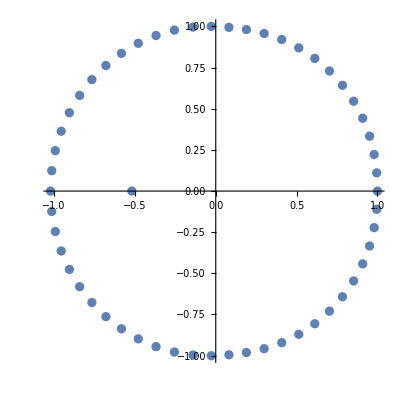

```mathematica
ListPlot[%,AspectRatio->Automatic]
```

(e)

```mathematica
poly=Sum[RandomComplex[] z^i,{i,0,100}]
```

(0.272828+0.545108 ⅈ)+(0.966999+0.266837 ⅈ) z+(0.800212+0.828803 ⅈ) z^2+(0.747092+0.774435 ⅈ) z^3+(0.561711+0.0469886 ⅈ) z^4+(0.875544+0.421834 ⅈ) z^5+(0.175706+0.169069 ⅈ) z^6+(0.70583+0.0567425 ⅈ) z^7+(0.604867+0.258934 ⅈ) z^8+(0.726323+0.536687 ⅈ) z^9+(0.629775+0.376271 ⅈ) z^10+(0.934587+0.143877 ⅈ) z^11+(0.624872+0.454279 ⅈ) z^12+(0.193864+0.403565 ⅈ) z^13+(0.704735+0.454093 ⅈ) z^14+(0.973431+0.185184 ⅈ) z^15+(0.689501+0.67993 ⅈ) z^16+(0.549514+0.492525 ⅈ) z^17+(0.0842212+0.387317 ⅈ) z^18+(0.428189+0.371515 ⅈ) z^19+(0.0865847+0.185702 ⅈ) z^20+(0.198257+0.462696 ⅈ) z^21+(0.721909+0.490723 ⅈ) z^22+(0.562534+0.969584 ⅈ) z^23+(0.472755+0.23048 ⅈ) z^24+(0.772709+0.788548 ⅈ) z^25+(0.836131+0.0487833 ⅈ) z^26+(0.858408+0.818579 ⅈ) z^27+(0.323902+0.115741 ⅈ) z^28+(0.540497+0.255361 ⅈ) z^29+(0.267006+0.000463859 ⅈ) z^30+(0.58111+0.447905 ⅈ) z^31+(0.672385+0.160857 ⅈ) z^32+(0.892804+0.919345 ⅈ) z^33+(0.845305+0.688506 ⅈ) z^34+(0.00735381+0.425528 ⅈ) z^35+(0.330332+0.368503 ⅈ) z^36+(0.438403+0.308952 ⅈ) z^37+(0.570144+0.027788 ⅈ) z^38+(0.383944+0.631267 ⅈ) z^39+(0.181195+0.693414 ⅈ) z^40+(0.0310312+0.239433 ⅈ) z^41+(0.469999+0.139524 ⅈ) z^42+(0.448603+0.579262 ⅈ) z^43+(0.942153+0.980561 ⅈ) z^44+(0.476692+0.107346 ⅈ) z^45+(0.226725+0.751385 ⅈ) z^46+(0.859926+0.0773985 ⅈ) z^47+(0.471313+0.256262 ⅈ) z^48+(0.559914+0.271035 ⅈ) z^49+(0.714955+0.168445 ⅈ) z^50+(0.217509+0.498283 ⅈ) z^51+(0.81097+0.949326 ⅈ) z^52+(0.0428496+0.00398984 ⅈ) z^53+(0.657289+0.676416 ⅈ) z^54+(0.70212+0.510425 ⅈ) z^55+(0.0647212+0.147052 ⅈ) z^56+(0.67413+0.206877 ⅈ) z^57+(0.269651+0.591549 ⅈ) z^58+(0.712306+0.642746 ⅈ) z^59+(0.470377+0.0133429 ⅈ) z^60+(0.849827+0.839052 ⅈ) z^61+(0.512187+0.837429 ⅈ) z^62+(0.756992+0.870164 ⅈ) z^63+(0.153466+0.932342 ⅈ) z^64+(0.923594+0.0477755 ⅈ) z^65+(0.572158+0.291537 ⅈ) z^66+(0.353608+0.701679 ⅈ) z^67+(0.963746+0.200405 ⅈ) z^68+(0.724823+0.866038 ⅈ) z^69+(0.558582+0.364859 ⅈ) z^70+(0.954648+0.469938 ⅈ) z^71+(0.254973+0.803809 ⅈ) z^72+(0.395734+0.393279 ⅈ) z^73+(0.442481+0.613077 ⅈ) z^74+(0.0378392+0.613088 ⅈ) z^75+(0.788593+0.399937 ⅈ) z^76+(0.813356+0.921429 ⅈ) z^77+(0.274845+0.532622 ⅈ) z^78+(0.234229+0.152845 ⅈ) z^79+(0.203965+0.406465 ⅈ) z^80+(0.659432+0.986454 ⅈ) z^81+(0.438503+0.188392 ⅈ) z^82+(0.938052+0.119975 ⅈ) z^83+(0.724506+0.173872 ⅈ) z^84+(0.210008+0.625089 ⅈ) z^85+(0.79416+0.905723 ⅈ) z^86+(0.993386+0.408739 ⅈ) z^87+(0.389653+0.740297 ⅈ) z^88+(0.619614+0.967125 ⅈ) z^89+(0.129813+0.816917 ⅈ) z^90+(0.586174+0.948524 ⅈ) z^91+(0.984988+0.0923531 ⅈ) z^92+(0.0708708+0.75036 ⅈ) z^93+(0.037442+0.916619 ⅈ) z^94+(0.149305+0.465516 ⅈ) z^95+(0.0398893+0.459658 ⅈ) z^96+(0.0885756+0.337506 ⅈ) z^97+(0.0810652+0.389725 ⅈ) z^98+(0.877266+0.271893 ⅈ) z^99+(0.146693+0.116434 ⅈ) z^100

```mathematica
roots=z/.NSolve[poly==0,z];
```

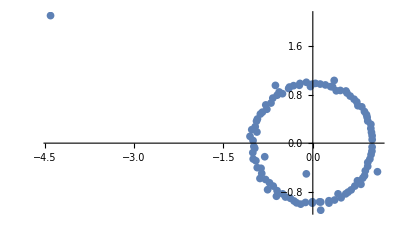

```mathematica
ListPlot[Table[{Re[z],Im[z]},{z,roots}],AspectRatio->Automatic]
```

```mathematica
poly=Sum[RandomComplex[] z^i,{i,0,1000}];
```

```mathematica
roots=z/.NSolve[poly==0,z];
```

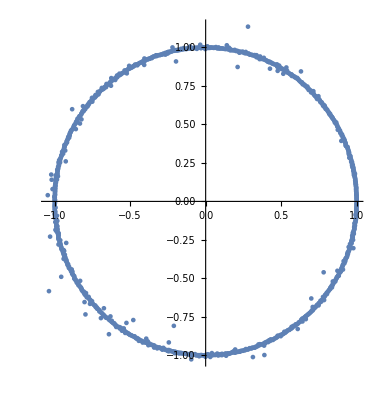

```mathematica
ListPlot[Table[{Re[z],Im[z]},{z,roots}],AspectRatio->Automatic]
```

### Exercise 5

```mathematica
M={{1,-1,1},{1,0,-1},{1,2,1}}
```

{{1,-1,1},{1,0,-1},{1,2,1}}

```mathematica
Eigenvalues[M]
```

{2,ⅈ √3,-ⅈ √3}

```mathematica
A=DiagonalMatrix[%]
```

{{2,0,0},{0,ⅈ √3,0},{0,0,-ⅈ √3}}

```mathematica
P=Transpose[Eigenvectors[M]]
```

{{1,-(-ⅈ+√3)/(-2 ⅈ+√3),-(ⅈ+√3)/(2 ⅈ+√3)},{0,-(-2 ⅈ-√3)/(-2 ⅈ+√3),-(2 ⅈ-√3)/(2 ⅈ+√3)},{1,1,1}}

```mathematica
M.P-P.A
```

{{0,1+(-2 ⅈ-√3)/(-2 ⅈ+√3)-(-ⅈ+√3)/(-2 ⅈ+√3)+(ⅈ √3 (-ⅈ+√3))/(-2 ⅈ+√3),1+(2 ⅈ-√3)/(2 ⅈ+√3)-(ⅈ+√3)/(2 ⅈ+√3)-(ⅈ √3 (ⅈ+√3))/(2 ⅈ+√3)},{0,-1+(ⅈ √3 (-2 ⅈ-√3))/(-2 ⅈ+√3)-(-ⅈ+√3)/(-2 ⅈ+√3),-1-(ⅈ √3 (2 ⅈ-√3))/(2 ⅈ+√3)-(ⅈ+√3)/(2 ⅈ+√3)},{0,1-ⅈ √3-(2 (-2 ⅈ-√3))/(-2 ⅈ+√3)-(-ⅈ+√3)/(-2 ⅈ+√3),1+ⅈ √3-(2 (2 ⅈ-√3))/(2 ⅈ+√3)-(ⅈ+√3)/(2 ⅈ+√3)}}

```mathematica
Simplify[%]
```

{{0,0,0},{0,0,0},{0,0,0}}

### Exercise 6

(a)

```mathematica
ode={y''[x]+x y[x]==0,y[0]==0,y'[0]==1}
```

{x y[x]+y''[x]==0,y[0]==0,y'[0]==1}

```mathematica
yfun=y/.NDSolve[ode,y,{x,0,20}][[1]]
```

InterpolatingFunction[{{0., 20.}}, <>]

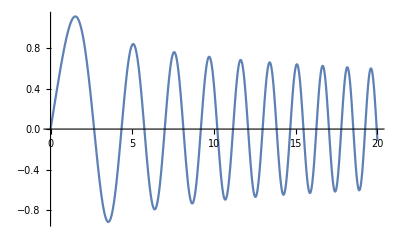

```mathematica
Plot[yfun[x],{x,0,20}]
```

(b) (i)

```mathematica
ode={x'[t]==y[t],y'[t]==(1-x[t]^2)y[t]-x[t],x[0]==1,y[0]==1};
{xfun,yfun}={x,y}/.NDSolve[ode,{x,y},{t,0,20}][[1]];
```

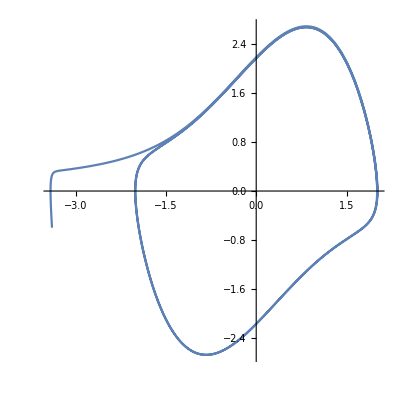

```mathematica
ParametricPlot[{xfun[t],yfun[t]},{t,0,20}]
```

(ii)

```mathematica
Manipulate[ode={x'[t]==y[t],y'[t]==(1-x[t]^2)y[t]-x[t],x[0]==p[[1]],y[0]==p[[2]]};
{xfun,yfun}={x,y}/.NDSolve[ode,{x,y},{t,0,20}][[1]];
ParametricPlot[{xfun[t],yfun[t]},{t,0,20},PlotRange->{{-4,4},{-4,4}},PlotLabel->"(x_0,y_0)="<>"("<>ToString[p[[1]]]<>","<>ToString[p[[2]]]<>")",Ticks->{{-2,-1,1,1},{-2,-1,1,2}}],{{p,{0.1,0.1}},Locator}]
```